### Hamiltonian written in the co basis

```mathematica
hco[n_,ρ_]:=Block[{F0=Fibonacci[n-2],F1=Fibonacci[n-1],F2=Fibonacci[n],tblw,tbls,ar},
tblw=Table[{i,i+F0}->ρ,{i,1,F1}];
tbls=Table[{i,i+F1}->1.,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

## n fixed, vary state (idos)

```mathematica
ρ=0.5;
n=20;
{val,vec}=Eigensystem[hco[n,ρ]];
```

```mathematica
o=Ordering[val];
val=val[[o]];
vec=vec[[o]];
```

```mathematica
Length[val]
```

6765

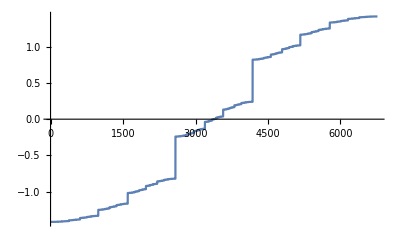

```mathematica
ListPlot[val,Joined->True]
```

```mathematica
(* chose a state *)
a=5000;
s=Abs[vec[[a]]];
(* random variable *)
x=Log[s];
```

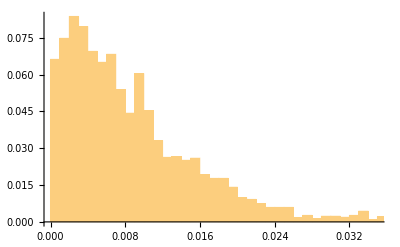

```mathematica
Histogram[s,Automatic,"Probability"]
```

```mathematica
{x0,σ}={Mean[x],StandardDeviation[x]};
```

```mathematica
logn[t_]:=Exp[-(t-x0)^2/(2σ)];
norm=1/Integrate[logn[t],{t,-10,0}];
```

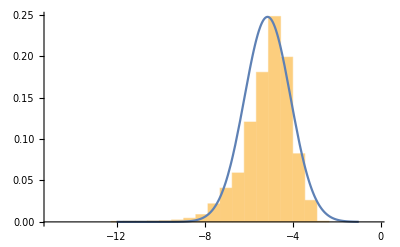

```mathematica
Histogram[x,{-15,0,0.55},"Probability",Epilog->First@Plot[0.65*norm logn[x],{x,-12,-1},PlotRange->All]]
```

```mathematica
{x0,σ}={Mean[x],StandardDeviation[x]};
```

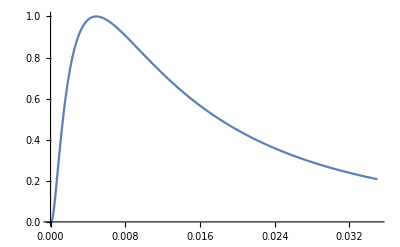

```mathematica
Plot[Exp[-(Log[x]-x0)^2/(2σ)],{x,0,0.035},PlotRange->All]
```

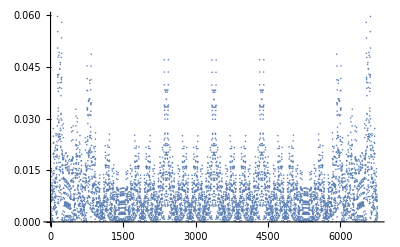

```mathematica
ListPlot[s,Joined->False,PlotRange->All]
```

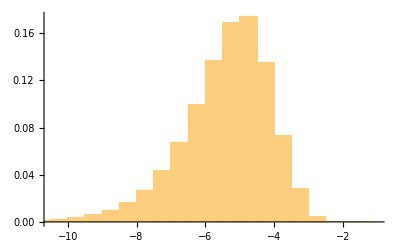

```mathematica
Histogram[Log[Abs[Flatten[vec]]],Automatic,"Probability"]
```

## idos fixed, vary n

```mathematica
ρ=0.5;
n=20;
{valp,vecp}=Eigensystem[hco[n,ρ]];
{val,vec}=Eigensystem[hco[n-1,ρ]];
```

```mathematica
o=Ordering[val];
val=val[[o]];
vec=vec[[o]];

o=Ordering[valp];
valp=valp[[o]];
vecp=vecp[[o]];

L=Fibonacci[n-1];
Lp=Fibonacci[n];

idos=Table[{val[[i]],N[i/L]},{i,L}];
idosp=Table[{valp[[i]],N[i/Lp]},{i,Lp}];
```

```mathematica
(* chose a gap ie an energy label on the small chain *)
g=2000;
(* corresponding energy label on the large chain *)
gp=Floor[g Lp/L];

(* the 2 corresponding states *)
s=Abs[vec[[g]]];
sp=Abs[vecp[[gp]]];
```

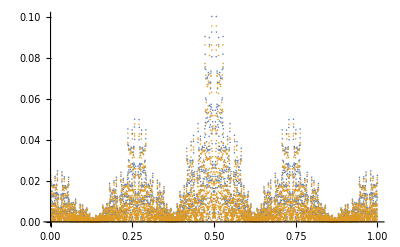

```mathematica
(* do the 2 states look different? *)
sx=Table[{i/L,s[[i]]},{i,L}];
spx=Table[{i/Lp,sp[[i]]},{i,Lp}];
ListPlot[{sx,spx},PlotRange->All]
```

```mathematica
Export[NotebookDirectory[]<>"data/consecutive_sizes_state.png",%,ImageSize->1000]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/data/consecutive_sizes_state.png

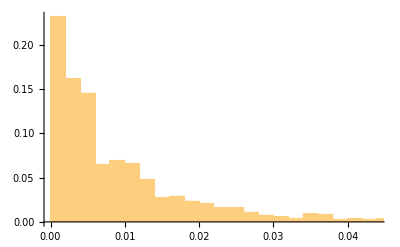
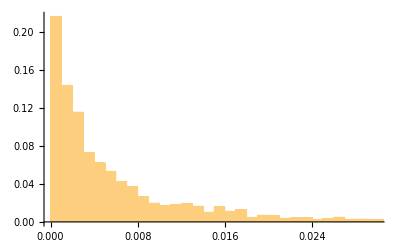

```mathematica
{Histogram[s,Automatic,"Probability"],Histogram[sp,Automatic,"Probability"]}
```

```mathematica
x=Log[s];
xp=Log[sp];
{x0,σ}={Mean[x],StandardDeviation[x]};
{x0p,σp}={Mean[xp],StandardDeviation[xp]};
```

```mathematica
logn[t_]:=Exp[-(t-x0)^2/(2σ)];
norm=1/Integrate[logn[t],{t,-10,0}];
lognp[t_]:=Exp[-(t-x0p)^2/(2σp)];
normp=1/Integrate[lognp[t],{t,-10,0}];
```

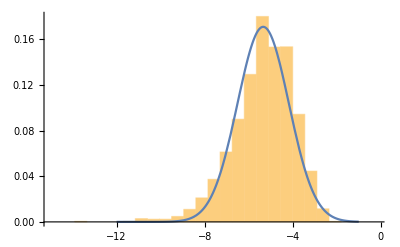

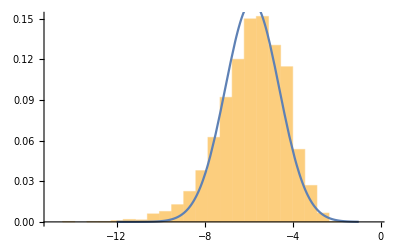

```mathematica
Histogram[x,{-15,0,0.55},"Probability",Epilog->First@Plot[0.5*norm logn[x],{x,-12,-1},PlotRange->All]]
Histogram[xp,{-15,0,0.55},"Probability",Epilog->First@Plot[0.5*normp lognp[x],{x,-12,-1},PlotRange->All]]
```

```mathematica
Export[NotebookDirectory[]<>"data/plogpsi.png",%,ImageSize->1000]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/data/plogpsi.png